## Pre

This is a calculation of the landscape of the MAA MZA solutions as a function of omega and k

Setting Defaults

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/dispersion-relation/landscape-lsa

```mathematica
Get["../../../neupackage/mma/dispersion-relation.wl"]
```

```mathematica
FileNames[]
```

{density-plot-landscape-lsa.nb,DR-sawyer-spectrum-SC1-01.m,DR-sawyer-spectrum-SC1-01.out,DR-sawyer-spectrum-SC2-01.m,DR-sawyer-spectrum-SC2-01.out,landscape-rok-sawyer-spectrum-SC1-01.m,landscape-rok-sawyer-spectrum-SC1-01.out,landscape-rok-sawyer-spectrum-SC1-01-parallel.m,landscape-rok-sawyer-spectrum-SC1-01-parallel.out,landscape-rok-sawyer-spectrum-SC2-01-parallel.m,landscape-rok-sawyer-spectrum-SC2-01-parallel.out,maalandscape-spectrum-sc1-rok-01.csv,maalandscape-spectrum-sc1-rok-01-parallel.csv,mzamlsalandscape-spectrum-sc1-rok-01.csv,mzamlsalandscape-spectrum-sc1-rok-01-parallel.csv,mzamlsalandscape-spectrum-sc2-rok-01-parallel.csv,mzamrealklsadata-box-spectrum-sc1-01.csv,mzaplsadata-box-spectrum-sc1-01.csv,mzaplsalandscape-spectrum-sc1-rok-01.csv,mzaplsalandscape-spectrum-sc1-rok-01-parallel.csv,mzaplsalandscape-spectrum-sc2-rok-01-parallel.csv,mzaprealklsadata-box-spectrum-sc1-01.csv}

Define Global Functions

```mathematica
pltDR[spect_]:=Show[
Plot[(#*x)&/@DeleteDuplicates@Flatten[{#[[1]]}&/@spectS],{x,-4.5,4.5},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,ImagePadding->{{20, 70}, {20, 20}},PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLabel->"Dispersion Relation for Spectrum "<>ToString[spect],AspectRatio->1],

ParametricPlot[
{
{n ConAxialSymOmegaNMAA[n,spect],ConAxialSymOmegaNMAA[n,spect]},
{n ConAxialSymOmegaNMZA[n,spect][[1]],ConAxialSymOmegaNMZA[n,spect][[1]]},
{n ConAxialSymOmegaNMZA[n,spect][[2]],ConAxialSymOmegaNMZA[n,spect][[2]]}
},
{n,-50,50},Frame->True,FrameLabel->{"k","ω"},ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLegends->Placed[{"MAA","MZA+","MZA-"},{Left,Top}],PlotLabel->"Dispersion Relation",Exclusions->{1/0.3,1/0.9,1/0.6}]
]
```

```mathematica
pltDRMAAData[spect_,stepsize_:0.01]:=Table[
{n ConAxialSymOmegaNMAA[n,spect],ConAxialSymOmegaNMAA[n,spect]},
{n,-50,50,stepsize}
]
```

```mathematica
pltDRMZApData[spect_,stepsize_:0.01]:=Table[
{n ConAxialSymOmegaNMZA[n,spect][[1]],ConAxialSymOmegaNMZA[n,spect][[1]]},
{n,-50,50,stepsize}
]
pltDRMZAmData[spect_,stepsize_:0.01]:=Table[
{n ConAxialSymOmegaNMZA[n,spect][[2]],ConAxialSymOmegaNMZA[n,spect][[2]]},
{n,-50,50,stepsize}
]
```

Define Spectra

```mathematica
uNueBarMin=Cos[ArcSin[0.93]]
alpha=0.77(1/0.93)^2
```

0.36756

0.890276

```mathematica
spectB={{{0,1},1}};
spectS={{{0,uNueBarMin},1},{{uNueBarMin,1},1-alpha}}
spectSC1={{{0,uNueBarMin},1},{{uNueBarMin,1},-0.1}}
spectSC2={{{0,uNueBarMin},1},{{uNueBarMin,1},-0.3}}
```

{{{0,0.36756},1},{{0.36756,1},0.109724}}

{{{0,0.36756},1},{{0.36756,1},-0.1}}

{{{0,0.36756},1},{{0.36756,1},-0.3}}

```mathematica
spectFunCos[u_]=Cos[u Pi/2]
```

Cos[(π u)/2]

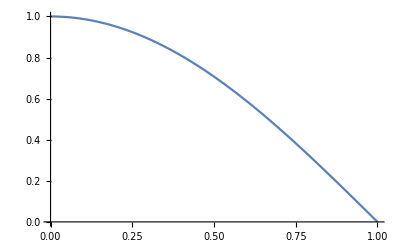

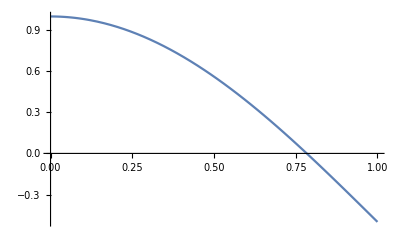

```mathematica
Plot[Cos[u Pi/2],{u,0,1}]
Plot[1.5Cos[u Pi/2]-0.5,{u,0,1}]
```

```mathematica
??SpectrumOmegaNMAA
```

dispersion`SpectrumOmegaNMAA

SpectrumOmegaNMAA[n_?NumberQ,ct1_?NumberQ,ct2_?NumberQ,spectrumFun_]:=1/4 (IntFun0nFSpect[n,ct1,ct2,spectrumFun]-IntFun2nFSpect[n,ct1,ct2,spectrumFun])

```mathematica
?Piecewise
```

Piecewise[{{val_1,cond_1},{val_2,cond_2},…}] represents a piecewise function with values val_i in the regions defined by the conditions cond_i. 
Piecewise[{{val_1,cond_1},…},val] uses default value val if none of the cond_i apply. The default for val is 0.

```mathematica
testF[u_]:=Piecewise[{{ Cos[u Pi/2] , 0≤u≤1} },0]
```

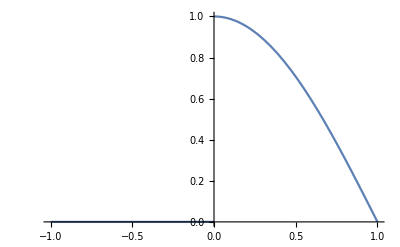

```mathematica
Plot[testF[u],{u,-1,1}]
```

## Plots

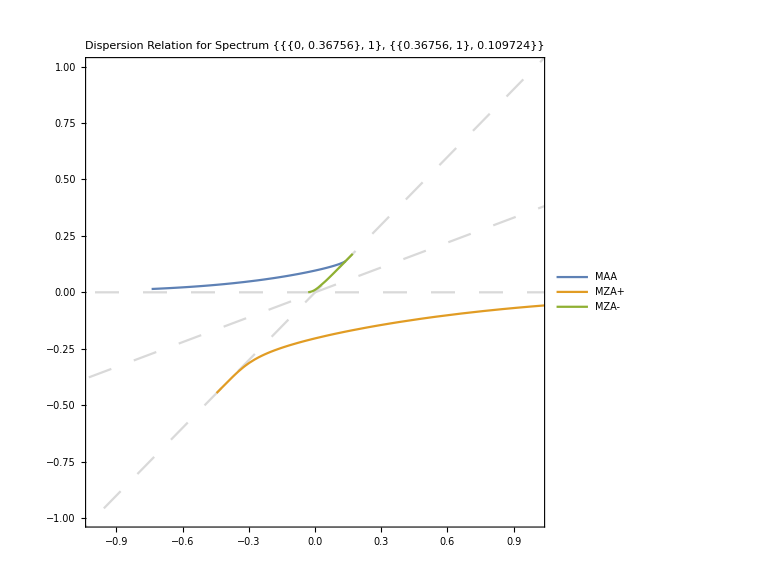

```mathematica
Show[
pltDR[spectS],
PlotRange->{{-1,1},{-1,1}}
]
```

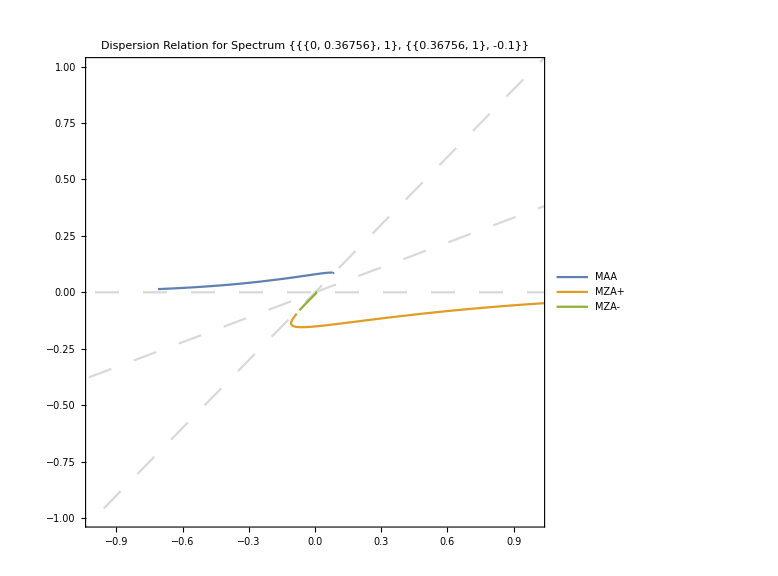

```mathematica
Show[
pltDR[spectSC1],
PlotRange->{{-1,1},{-1,1}}
]
```

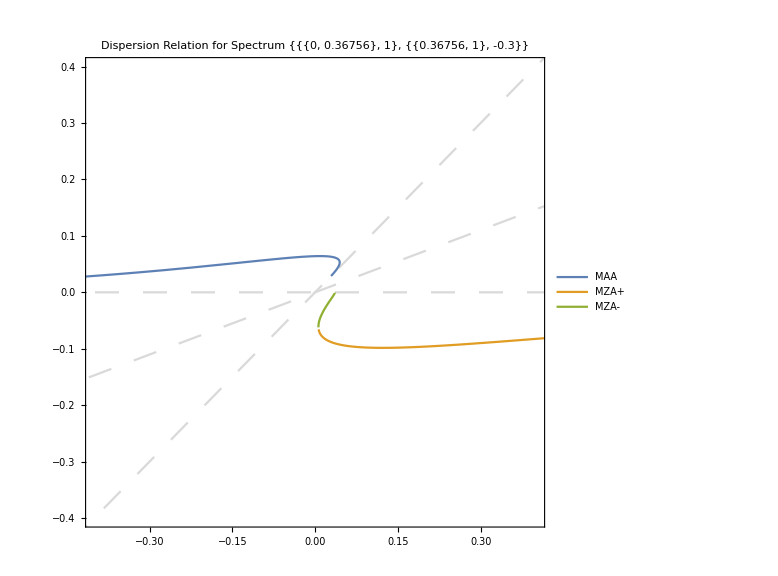

```mathematica
Show[
pltDR[spectSC2],
PlotRange->{{-0.4,0.4},{-0.4,0.4}}
]
```

Verify

```mathematica
maaSC1Verify=Table[
{n ConAxialSymOmegaNMAA[n,spectSC1],ConAxialSymOmegaNMAA[n,spectSC1]},
{n,-0.9,0.9,0.09}
]//Quiet
```

{{-0.063785,0.0708722},{-0.0580578,0.0716763},{-0.0522008,0.0725011},{-0.0462087,0.0733471},{-0.0400759,0.0742146},{-0.0337967,0.0751038},{-0.0273653,0.0760146},{-0.0207756,0.0769468},{-0.0140219,0.0778994},{-0.00709842,0.0788714},{-6.85258×10^14,6.17225×10^30},{0.00727765,0.0808628},{0.0147373,0.0818738},{0.0223791,0.0828854},{0.0301989,0.0838858},{0.0381854,0.0848564},{0.0463149,0.0857683},{0.0545409,0.0865729},{0.0627726,0.0871841},{0.0708186,0.0874304},{0.0782005,0.0868894}}

```mathematica
Abs@ConAxialSymOmegaNMAAEqnLHSComplex[#[[2]],#[[1]],spectSC1]&/@maaSC1Verify
```

{1.38778×10^-17,0.,1.38778×10^-17,0.,5.55112×10^-17,1.38778×10^-17,0.,0.,8.32667×10^-17,0.,0.,0.,0.,0.,1.38778×10^-17,3.19189×10^-16,0.,0.,0.,0.,1.38778×10^-17}

```mathematica
mzamSC1Verify=Table[
{n ConAxialSymOmegaNMZA[n,spectSC1][[2]],ConAxialSymOmegaNMZA[n,spectSC1][[2]]},
{n,-0.9,0.9,0.09}
]//Quiet
```

{{0.00391376,-0.00434863},{0.00371731,-0.00458927},{0.00349518,-0.00485442},{0.00324319,-0.00514793},{0.00295624,-0.00547451},{0.002628,-0.00584},{0.0022506,-0.00625167},{0.00181406,-0.00671876},{0.00130557,-0.00725316},{0.000708341,-0.00787045},{0.,0.},{-0.000850045,-0.00944495},{-0.00188482,-0.0104712},{-0.00316695,-0.0117294},{-0.00479165,-0.0133101},{-0.00691191,-0.0153598},{-0.00979245,-0.0181342},{-0.013942,-0.0221302},{-0.0205119,-0.0284888},{-0.0330446,-0.0407958},{-0.0782005+0.0208912 ⅈ,-0.0868894+0.0232124 ⅈ}}

```mathematica
Abs@ConAxialSymOmegaNMZAmEqnLHSComplex[#[[2]],#[[1]],spectSC1]&/@(mzamSC1Verify)
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{0.0189337,0.0191286,0.0193202,0.0195068,0.0196863,0.019856,0.0200126,0.0201515,0.020267,0.0203516,Indeterminate,0.0203838,0.0202983,0.020111,0.0197807,0.0192426,0.0183872,0.0170071,0.0146238,0.0094884,0.0189723}

## Data Production

## SC1

```mathematica
maalandscapeROKSC101=Import["maalandscape-spectrum-sc1-rok-01.csv"]
```

{{-1.,-1.,Indeterminate},{-1.,-0.996667,-1.0828},{-1.,-0.993333,-1.08323},{-1.,-0.99,-1.08357},811793,{2.,1.99,1.91697},{2.,1.99333,1.9172},{2.,1.99667,1.91747},{2.,2.,Indeterminate}}
 |  |  |  |

```mathematica
mzaplandscapeROKSC101=Import["mzaplsalandscape-spectrum-sc1-rok-01.csv"]
```

{{-1.,-1.,Indeterminate},{-1.,-0.996667,-0.9236092044146207+0.1664969447373949*I},{-1.,-0.993333,-0.9234082873458697+0.1481882308596958*I},811796,{2.,1.99667,2.076263056229772+0.1832965768759167*I},{2.,2.,Indeterminate}}
 |  |  |  |

```mathematica
mzamlandscapeROKSC101=Import["mzamlsalandscape-spectrum-sc1-rok-01.csv"]
```

{{-1.,-1.,Indeterminate},{-1.,-0.996667,-0.9236092044146207-0.1664969447373949*I},{-1.,-0.993333,-0.9234082873458697-0.1481882308596958*I},811796,{2.,1.99667,2.076263056229772-0.1832965768759167*I},{2.,2.,Indeterminate}}
 |  |  |  |

## Cos Spectra

```mathematica
maalandscapeROKCosC01=Import["maalandscape-spectrum-cos-c-rok-01.csv"]
```

{{-4.499,-4.499,SpectrumOmegaKMAAEqnLHS[omegareal,0, kreal,0, spectFunCos]},{-4.499,-4.489,SpectrumOmegaKMAAEqnLHS[omegareal,0, kreal,0, spectFunCos]},809997,{4.491,4.491,SpectrumOmegaKMAAEqnLHS[omegareal,0, kreal,0, spectFunCos]}}
 |  |  |  |

```mathematica
SpectrumOmegaKMAAEqnLHS[0.1,0,0.1,0,spectFunCos]
```

{-0.21831,0}

```mathematica
maalandscapeROKCosC01[[100]]
```

{-4.499,-3.509,SpectrumOmegaKMAAEqnLHS[omegareal,0, kreal,0, spectFunCos]}

```mathematica
Dimensions@maalandscapeROKCosC01
```

{810000,7}

```mathematica
Dimensions@maalandscapeROKSC101
```

{811801,3}

## Sawyer

```mathematica
maalandscapeROKS01=Import["maalandscape-spectrum-s-rok-01.csv"]
```

{{-1.,-1.,Indeterminate},{-1.,-0.996667,-1.13708},{-1.,-0.993333,-1.13642},{-1.,-0.99,-1.13584},811793,{2.,1.99,1.86326},{2.,1.99333,1.86292},{2.,1.99667,1.86253},{2.,2.,Indeterminate}}
 |  |  |  |

```mathematica
mzaplandscapeROKS01=Import["mzaplsalandscape-spectrum-s-rok-01.csv"]
```

{{-1.,-1.,Indeterminate},{-1.,-0.996667,-0.562703},{-1.,-0.993333,-0.582924},{-1.,-0.99,-0.595385},811793,{2.,1.99,2.42563},{2.,1.99333,2.4373},{2.,1.99667,2.45631},{2.,2.,Indeterminate}}
 |  |  |  |

```mathematica
mzamlandscapeROKS01=Import["mzamlsalandscape-spectrum-s-rok-01.csv"]
```

{{-1.,-1.,Indeterminate},{-1.,-0.996667,-1.21982},{-1.,-0.993333,-1.20036},{-1.,-0.99,-1.18856},811793,{2.,1.99,1.79146},{2.,1.99333,1.78018},{2.,1.99667,1.7616},{2.,2.,Indeterminate}}
 |  |  |  |

```mathematica
Dimensions@maalandscapeROKS01
```

{811801,3}

Clean Up Data

## SC1

```mathematica
maalandscapeROKSC101Clean=Select[
{ToExpression@#[[2]],ToExpression@#[[1]],Abs@ToExpression@#[[3]]}&/@maalandscapeROKSC101,
NumberQ@#[[3]]&];
```

```mathematica
mzaplandscapeROKSC101Clean=Select[
{ToExpression@#[[2]],ToExpression@#[[1]],Abs@ToExpression@#[[3]]}&/@mzaplandscapeROKSC101,
NumberQ@#[[3]]&];
```

```mathematica
mzamlandscapeROKSC101Clean=Select[
{ToExpression@#[[2]],ToExpression@#[[1]],Abs@ToExpression@#[[3]]}&/@mzamlandscapeROKSC101,
NumberQ@#[[3]]&];
```

## Cos Spectra

```mathematica
maalandscapeROKCosC01Clean=Select[
{ToExpression@#[[2]],ToExpression@#[[1]],Abs@ToExpression@#[[3]]}&/@maalandscapeROKCosC01,
NumberQ@#[[3]]&];
```

ToExpression::sntxi: Incomplete expression; more input is needed .

General::stop: Further output of ToExpression::sntxi
     will be suppressed during this calculation.

$Aborted

## Sawyer

```mathematica
maalandscapeROKS01Clean=Select[
{ToExpression@#[[2]],ToExpression@#[[1]],Abs@ToExpression@#[[3]]}&/@maalandscapeROKS01,
NumberQ@#[[3]]&];
```

```mathematica
mzaplandscapeROKS01Clean=Select[
{ToExpression@#[[2]],ToExpression@#[[1]],Abs@ToExpression@#[[3]]}&/@mzaplandscapeROKS01,
NumberQ@#[[3]]&];
```

```mathematica
mzamlandscapeROKS01Clean=Select[
{ToExpression@#[[2]],ToExpression@#[[1]],Abs@ToExpression@#[[3]]}&/@mzamlandscapeROKS01,
NumberQ@#[[3]]&];
```

Data Export

Export DR data

## SC1

```mathematica
pltDRMAADataSC1=Select[pltDRMAAData[spectSC1,0.01],#[[1]]∈Reals&];//Quiet
```

```mathematica
pltDRMZApDataSC1=Select[pltDRMZApData[spectSC1,0.001],#[[1]]∈Reals&];//Quiet
```

```mathematica
pltDRMZAmDataSC1=Select[pltDRMZAmData[spectSC1,0.001],#[[1]]∈Reals&];//Quiet
```

```mathematica
Export["cleanup/pltDRMAADataSC1.csv",pltDRMAADataSC1]
Export["cleanup/pltDRMZApDataSC1.csv",pltDRMZApDataSC1]
Export["cleanup/pltDRMZAmDataSC1.csv",pltDRMZAmDataSC1]
```

cleanup/pltDRMAADataSC1.csv

cleanup/pltDRMZApDataSC1.csv

cleanup/pltDRMZAmDataSC1.csv

Export Landscape of DR plane

```mathematica
Export["cleanup/maalandscape-spectrum-sc1-rok-01-clean.csv",maalandscapeROKSC101Clean]
```

cleanup/maalandscape-spectrum-sc1-rok-01-clean.csv

```mathematica
Export["cleanup/mzaplandscape-spectrum-sc1-rok-01-clean.csv",mzaplandscapeROKSC101Clean]
```

cleanup/mzaplandscape-spectrum-sc1-rok-01-clean.csv

```mathematica
Export["cleanup/mzamlandscape-spectrum-sc1-rok-01-clean.csv",mzamlandscapeROKSC101Clean]
```

cleanup/mzamlandscape-spectrum-sc1-rok-01-clean.csv

## Sawyer

```mathematica
pltDRMAADataS=Select[pltDRMAAData[spectS,0.01],#[[1]]∈Reals&];//Quiet
```

```mathematica
pltDRMZApDataS=Select[pltDRMZApData[spectS,0.01],#[[1]]∈Reals&];//Quiet
```

```mathematica
pltDRMZAmDataS=Select[pltDRMZAmData[spectS,0.01],#[[1]]∈Reals&];//Quiet
```

```mathematica
Export["cleanup/pltDRMAADataS.csv",pltDRMAADataS]
Export["cleanup/pltDRMZApDataS.csv",pltDRMZApDataS]
Export["cleanup/pltDRMZAmDataS.csv",pltDRMZAmDataS]
```

cleanup/pltDRMAADataS.csv

cleanup/pltDRMZApDataS.csv

cleanup/pltDRMZAmDataS.csv

```mathematica
Export["cleanup/maalandscape-spectrum-s-rok-01-clean.csv",maalandscapeROKS01Clean]
```

cleanup/maalandscape-spectrum-s-rok-01-clean.csv

```mathematica
Export["cleanup/mzaplandscape-spectrum-s-rok-01-clean.csv",mzaplandscapeROKS01Clean]
Export["cleanup/mzamlandscape-spectrum-s-rok-01-clean.csv",mzamlandscapeROKS01Clean]
```

cleanup/mzaplandscape-spectrum-s-rok-01-clean.csv

cleanup/mzamlandscape-spectrum-s-rok-01-clean.csv

Data Test

```mathematica
stepsize=0.99
```

0.99

```mathematica
Dimensions@maalandscapeROKSC101
```

{811801,3}

```mathematica
Dimensions@maalandscapeROKSC101Clean
```

{811414,3}

```mathematica
Dimensions@Select[maalandscapeROKSC101Clean,#[[3]]∈Reals&]
```

{811414,3}

```mathematica
Sort[maalandscapeROKSC101Clean,Abs@#1[[3]]<Abs@#[[3]]&]//Last
```

{-0.996667,-1.,1.0828}

```mathematica
Log@0.07955059145829596
```

-2.53136

```mathematica
maalandscapeROKSC101CleanPlt=ListDensityPlot[{#[[1]],#[[2]],Log@#[[3]]}&/@maalandscapeROKSC101Clean[[;;;;10]],PlotLegends->Automatic,PlotRange->{Automatic,Automatic,{-10,3}}]
```

```mathematica
Grid@{{
Show[maalandscapeROKSC101CleanPlt,
Show[pltDR[spectSC1],PlotRange->{{-1,2},{-1,2}}],ImageSize->Large
],
Show[pltDR[spectSC1],PlotRange->{{-1,2},{-1,2}}]
}}
```

```mathematica
Table[{omega,kreal,ConAxialSymOmegaNMAAEqnLHSComplex[omega,kreal+I kimag,spectS],kimag},{omega,-1,2,stepsize},{kreal,-0.9,1.9,stepsize},{kimag,0,2.9,stepsize}]
```

{{{{-1.,-0.9,-1.12704+0. ⅈ,0.},{-1.,-0.9,-1.10525+0.0315026 ⅈ,0.99},{-1.,-0.9,-1.08651+0.0418119 ⅈ,1.98}},{{-1.,0.09,-1.09459+0. ⅈ,0.},{-1.,0.09,-1.08942+0.0174824 ⅈ,0.99},{-1.,0.09,-1.07936+0.0283389 ⅈ,1.98}},{{-1.,1.08,-1.07952+0. ⅈ,0.},{-1.,1.08,-1.07725+0.0112921 ⅈ,0.99},{-1.,1.08,-1.07173+0.0200823 ⅈ,1.98}}},{{{-0.01,-0.9,-0.000389144-0.00872557 ⅈ,0.},{-0.01,-0.9,-0.00829748+0.00823887 ⅈ,0.99},{-0.01,-0.9,-0.00999818+0.00551763 ⅈ,1.98}},{{-0.01,0.09,-0.0507572+0. ⅈ,0.},{-0.01,0.09,-0.0144522+0.00867748 ⅈ,0.99},{-0.01,0.09,-0.0121486+0.00531158 ⅈ,1.98}},{{-0.01,1.08,-0.0185717+0. ⅈ,0.},{-0.01,1.08,-0.0158664+0.00369097 ⅈ,0.99},{-0.01,1.08,-0.013377+0.00373733 ⅈ,1.98}}},{{{0.98,-0.9,0.898485+0. ⅈ,0.},{0.98,-0.9,0.901125-0.0122481 ⅈ,0.99},{0.98,-0.9,0.907356-0.0214665 ⅈ,1.98}},{{0.98,0.09,0.88161+0. ⅈ,0.},{0.98,0.09,0.888095-0.0195493 ⅈ,0.99},{0.98,0.09,0.899675-0.0306682 ⅈ,1.98}},{{0.98,1.08,0.83541-0.0138106 ⅈ,0.},{0.98,1.08,0.872027-0.0362942 ⅈ,0.99},{0.98,1.08,0.893147-0.0455587 ⅈ,1.98}}},{{{1.97,-0.9,1.8819+0. ⅈ,0.},{1.97,-0.9,1.88292-0.00784551 ⅈ,0.99},{1.97,-0.9,1.88566-0.0148339 ⅈ,1.98}},{{1.97,0.09,1.87262+0. ⅈ,0.},{1.97,0.09,1.8744-0.0104135 ⅈ,0.99},{1.97,0.09,1.87873-0.0189958 ⅈ,1.98}},{{1.97,1.08,1.85923+0. ⅈ,0.},{1.97,1.08,1.86333-0.0151648 ⅈ,0.99},{1.97,1.08,1.87081-0.0253714 ⅈ,1.98}}}}

```mathematica
Table[
Sort[
Flatten[Out[282],1][[i]],Abs[#1[[3]]]<Abs[#2[[3]]]&
][[1]],
{i,1,Length@Out[282]}
]
```

{{-1.,-0.9,-1.07952,1.98},{-1.,0.09,-1.06964,1.98},{-1.,1.08,-1.06245,1.98},{-0.01,-0.9,-0.000389144-0.00872557 ⅈ,0.}}

```mathematica
Table[{omega,kreal,ConAxialSymOmegaNMZAEqnLHSComplex[omega,kreal+I kimag,spectS],kimag},{omega,-1,2,stepsize},{kreal,-0.9,1.9,stepsize},{kimag,0,2.9,stepsize}]

Table[{omega,kreal,ConAxialSymOmegaNMZApEqnLHSComplex[omega,kreal+I kimag,spectS],kimag},{omega,-1,2,stepsize},{kreal,-0.9,1.9,stepsize},{kimag,0,2.9,stepsize}]
```

{{{{-1.,-0.9,12.1075+0. ⅈ,0.},{-1.,-0.9,13.0361+0.955731 ⅈ,0.99},{-1.,-0.9,13.5815+1.20059 ⅈ,1.98}},{{-1.,0.09,13.2895+0. ⅈ,0.},{-1.,0.09,13.4583+0.516481 ⅈ,0.99},{-1.,0.09,13.7605+0.813463 ⅈ,1.98}},{{-1.,1.08,13.7357+0. ⅈ,0.},{-1.,1.08,13.8048+0.325737 ⅈ,0.99},{-1.,1.08,13.968+0.572669 ⅈ,1.98}}},{{{-0.01,-0.9,0.00357708-0.00196022 ⅈ,0.},{-0.01,-0.9,0.00231911+0.00212924 ⅈ,0.99},{-0.01,-0.9,0.00172616+0.00158751 ⅈ,1.98}},{{-0.01,0.09,-0.0297675+0. ⅈ,0.},{-0.01,0.09,0.000761849+0.00293889 ⅈ,0.99},{-0.01,0.09,0.00110563+0.00166601 ⅈ,1.98}},{{-0.01,1.08,-0.00144896+0. ⅈ,0.},{-0.01,1.08,-0.000246128+0.00138045 ⅈ,0.99},{-0.01,1.08,0.000622296+0.00124898 ⅈ,1.98}}},{{{0.98,-0.9,17.4119+0. ⅈ,0.},{0.98,-0.9,17.3673+0.259558 ⅈ,0.99},{0.98,-0.9,17.2502+0.474835 ⅈ,1.98}},{{0.98,0.09,17.7346+0. ⅈ,0.},{0.98,0.09,17.6563+0.377192 ⅈ,0.99},{0.98,0.09,17.4501+0.656665 ⅈ,1.98}},{{0.98,1.08,18.5604-0.604476 ⅈ,0.},{0.98,1.08,18.0824+0.63779 ⅈ,0.99},{0.98,1.08,17.6621+0.96408 ⅈ,1.98}}},{{{1.97,-0.9,66.6197+0. ⅈ,0.},{1.97,-0.9,66.5816+0.349195 ⅈ,0.99},{1.97,-0.9,66.4748+0.671362 ⅈ,1.98}},{{1.97,0.09,67.0183+0. ⅈ,0.},{1.97,0.09,66.9608+0.441079 ⅈ,0.99},{1.97,0.09,66.8036+0.834093 ⅈ,1.98}},{{1.97,1.08,67.536+0. ⅈ,0.},{1.97,1.08,67.4446+0.586061 ⅈ,0.99},{1.97,1.08,67.1931+1.07533 ⅈ,1.98}}}}

{{{{-1.,-0.9,-0.676752+0. ⅈ,0.},{-1.,-0.9,-0.772254-0.082303 ⅈ,0.99},{-1.,-0.9,-0.817239-0.0981564 ⅈ,1.98}},{{-1.,0.09,-0.788721+0. ⅈ,0.},{-1.,0.09,-0.804117-0.0433342 ⅈ,0.99},{-1.,0.09,-0.82994-0.0664474 ⅈ,1.98}},{{-1.,1.08,-0.826199+0. ⅈ,0.},{-1.,1.08,-0.832164-0.0266873 ⅈ,0.99},{-1.,1.08,-0.845939-0.0463828 ⅈ,1.98}}},{{{-0.01,-0.9,-0.00736383-0.000203473 ⅈ,0.},{-0.01,-0.9,-0.00898541+0.00130926 ⅈ,0.99},{-0.01,-0.9,-0.00963542+0.000932285 ⅈ,1.98}},{{-0.01,0.09,0.0760465+0. ⅈ,0.},{-0.01,0.09,-0.00102002-0.0179107 ⅈ,0.99},{-0.01,0.09,-0.00568278-0.0109058 ⅈ,1.98}},{{-0.01,1.08,0.00764491+0. ⅈ,0.},{-0.01,1.08,0.00201483-0.00763032 ⅈ,0.99},{-0.01,1.08,-0.00312361-0.00768948 ⅈ,1.98}}},{{{0.98,-0.9,1.1586+0. ⅈ,0.},{0.98,-0.9,1.15157+0.0291062 ⅈ,0.99},{0.98,-0.9,1.13595+0.0496601 ⅈ,1.98}},{{0.98,0.09,1.20136+0. ⅈ,0.},{0.98,0.09,1.18134+0.0489409 ⅈ,0.99},{0.98,0.09,1.15174+0.0719161 ⅈ,1.98}},{{0.98,1.08,1.32003+0.125908 ⅈ,0.},{0.98,1.08,1.21116+0.0940708 ⅈ,0.99},{0.98,1.08,1.16254+0.106377 ⅈ,1.98}}},{{{1.97,-0.9,2.16475+0. ⅈ,0.},{1.97,-0.9,2.16179+0.0194108 ⅈ,0.99},{1.97,-0.9,2.15418+0.0359853 ⅈ,1.98}},{{1.97,0.09,2.18865+0. ⅈ,0.},{1.97,0.09,2.18281+0.027154 ⅈ,0.99},{1.97,0.09,2.16996+0.0474362 ⅈ,1.98}},{{1.97,1.08,2.22732+0. ⅈ,0.},{1.97,1.08,2.21026+0.0434579 ⅈ,0.99},{1.97,1.08,2.18674+0.0653702 ⅈ,1.98}}}}